```mathematica
(*Old version*)
```

```mathematica
meanFit1old=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1]
meanFit2old=FullSimplify[D[Log[(1-w)(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+w(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2]]
```

(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) rmax w (θ1-μ1) τ)/((σ^2+τ^2)^(3/2) ((ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2))) rmax (1-w) τ)/(√(σ^2+τ^2))+(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) rmax w τ)/(√(σ^2+τ^2))))

(θ2-μ2)/((1+ⅇ^(((2 θ2-μ1-μ2) (μ1-μ2))/(2 (σ^2+τ^2))) (-1+1/w)) (σ^2+τ^2))

```mathematica
(*Revised Version*)
```

(θ-w1 μ1-(1-w1) μ2)/(σ^2+τ^2)

```mathematica
meanFit1=FullSimplify[D[Log[(ⅇ^(-(θ1-(w1*μ1+(1-w1)*μ2))^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ1]]
meanFit2=FullSimplify[D[Log[(ⅇ^(-(θ2-((1-w2)*μ1+w2*μ2))^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2]]
```

(w1 (θ1-w1 μ1+(-1+w1) μ2))/(σ^2+τ^2)

(w2 (θ2+(-1+w2) μ1-w2 μ2))/(σ^2+τ^2)

```mathematica
(* What we need to use instead *)
D[Log[(ⅇ^(-(θ-μ)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ]/.{μ->(w1*μ1+(1-w1)*μ2)}
```

(θ-w1 μ1-(1-w1) μ2)/(σ^2+τ^2)

```mathematica
D[Log[(ⅇ^(-(θ-μ)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))*Exp[-beta*((1-m)*N1+m*N2)]],μ]/.{μ->(((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(1-((1-m)*N1)/((1-m)*N1+m*N2))*μ2)}
```

(θ-((1-m) N1 μ1)/((1-m) N1+m N2)-(1-((1-m) N1)/((1-m) N1+m N2)) μ2)/(σ^2+τ^2)

```mathematica
Fitness3=FullSimplify[%]
```

(ⅇ^Z rmax ((-1+m) N1 (θ-μ1)+m N2 (-θ+μ2)) τ)/((σ^2+τ^2) (ⅇ^Z ((-1+m) N1-m N2) rmax τ+ⅇ^(beta (N1-m N1+m N2)+Z+((-1+m) N1 (θ-μ1)+m N2 (-θ+μ2))^2/(2 (N1-m N1+m N2)^2 (σ^2+τ^2))) N1 √(σ^2+τ^2)+ⅇ^(beta (N1-m N1+m N2)+((-1+m) N1 (θ-μ1)+m N2 (-θ+μ2))^2/(2 (N1-m N1+m N2)^2 (σ^2+τ^2))) ((-1+m) N1-m N2) √(σ^2+τ^2)))

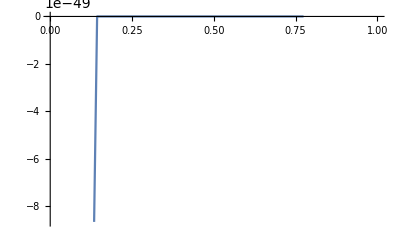

```mathematica
Block[{rmax=2,θ=0,μ1=-1,μ2=3,σ=1,τ=1,Z=0.5,N1=1000,N2=10,m=0.1},
Plot[Fitness3,{beta,0.001,1}]
]
```

```mathematica
Show[{
Plot3D[meanFit1old/.{σ->1,τ->1,θ1->5,w->0.5},{μ1,0,10},{μ2,0,10},AxesLabel->{μ1,μ2,"Selection Strength"},PlotStyle->Green],
Plot3D[meanFit1/.{σ->1,τ->1,θ1->5,w->0.5},{μ1,0,10},{μ2,0,10},AxesLabel->{μ1,μ2,"Selection Strength"}]
}]
Show[{
Plot3D[meanFit2old/.{σ->1,τ->1,θ2->5,w->0.5},{μ1,0,10},{μ2,0,10},AxesLabel->{μ1,μ2,"Selection Strength"},PlotStyle->Green],
Plot3D[meanFit2/.{σ->1,τ->1,θ2->5,w->0.5},{μ1,0,10},{μ2,0,10},AxesLabel->{μ1,μ2,"Selection Strength"}]
}]
```

-Graphics3D-

-Graphics3D-